```mathematica
SetDirectory[NotebookDirectory[]];
```

## 矩阵构建

```mathematica
ClearAll["`*"]
v=1;
i=PauliMatrix[0];x=PauliMatrix[1];y=PauliMatrix[2];z=PauliMatrix[3];
g1=KroneckerProduct[x,x];g2=KroneckerProduct[x,y];g3=KroneckerProduct[x,z];
g4=KroneckerProduct[y,i];g5=KroneckerProduct[z,i];
g13=1/(2I)(g1.g3-g3.g1);g12=1/(2I)(g1.g2-g2.g1);
U[ϕ_,θ_]:=MatrixExp[I g13 θ/2].MatrixExp[I g12 ϕ/2](*旋转矩阵*)
H=v(kx g1+ky g2-kz g3)+(m01+m1/2(kx^2+ky^2)-m2/2 kz^2)g5;(*正常态哈密顿量*)

coor2=U[ϕ,θ].H.FullSimplify[ConjugateTranspose[U[ϕ,θ]],Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]];(*坐标变换矩阵*)
(*coorTF=FullSimplify[tranForm,Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]];(*符号化简变换矩阵*)
coorTFCC=FullSimplify[FullSimplify[ConjugateTranspose[coorTF],Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]],Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]];(*符号化简变换矩阵的幺正形式*)

coor2=coorTF.H.coorTFCC;*)
HTr=FullSimplify[coor2,Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]&&Element[m01,Reals]&&Element[m1,Reals]&&Element[m2,Reals]];
```

```mathematica
MatrixForm[g3]
HTr[[1]][[3]]//Expand(*验证g3这一项的正确性*)
```

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)

-kz Cos[θ]-kx Cos[ϕ] Sin[θ]-ky Sin[θ] Sin[ϕ]

### 坐标变化(k_3-->G3)

```mathematica
nvec=Transpose[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}];
kvec={{kx,ky,kz}};
k3=kvec.nvec//Flatten(*k3在文章中表达式*)
```

{kz Cos[θ]+kx Cos[ϕ] Sin[θ]+ky Sin[θ] Sin[ϕ]}

### 坐标变化(G5)

```mathematica
MatrixForm[g5]
HTr[[1]][[1]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

m01+1/2 ((kx^2+ky^2) m1-kz^2 m2)

### 欧拉转动矩阵

```mathematica
ClearAll["`*"]
eulerAng=EulerMatrix[{0,-ϕ,-θ}];(*欧拉角转动*)
kvec1=Transpose[{{Subscript[k, x],Subscript[k, y],Subscript[k, z]}}];
{k11,k22,k33}=Flatten[eulerAng.kvec1];(*通过欧拉角转动计算任意角度转动的坐标(Subscript[k, 1],Subscript[k, 2],Subscript[k, 3])*)
kvec2=Transpose[{{k1,k2,k3}}];
{kx,ky,kz}=FullSimplify[Inverse[eulerAng].kvec2]//Flatten;
re=TrigReduce@Expand[(m01+1/2 ((kx^2+ky^2) m1-kz^2 m2))]
Collect[re,k1^2][[1]](*计算(6)中m1~*)
```

1/4 (4 m01+k1^2 m1+2 k2^2 m1+k3^2 m1-k1^2 m2-k3^2 m2+k1^2 m1 Cos[2 ϕ]-k3^2 m1 Cos[2 ϕ]+k1^2 m2 Cos[2 ϕ]-k3^2 m2 Cos[2 ϕ]+2 k1 k3 m1 Sin[2 ϕ]+2 k1 k3 m2 Sin[2 ϕ])

1/4 k1^2 (m1-m2+m1 Cos[2 ϕ]+m2 Cos[2 ϕ])

```mathematica
Simplify[1+Cos[2ϕ]]
Simplify[1-Cos[2ϕ]]
```

2 Cos[ϕ]^2

2 Sin[ϕ]^2

```mathematica
Collect[re,k3*k1][[2]](*计算(6)中m13*)
```

1/4 k1 k3 (2 m1 Sin[2 ϕ]+2 m2 Sin[2 ϕ])

```mathematica
Collect[re,k2^2][[1]](*计算(6)中m1/2*)
```

(k2^2 m1)/2

## 补充计算

```mathematica
ClearAll["`*"]
i=PauliMatrix[0];x=PauliMatrix[1];y=PauliMatrix[2];z=PauliMatrix[3];
g1=KroneckerProduct[x,x];
g2=KroneckerProduct[x,y];
g3=KroneckerProduct[x,z];
g5=KroneckerProduct[z,i];
g13=1/(2I)(g1.g3-g3.g1);
g12=1/(2I)(g1.g2-g2.g1);
rot=MatrixExp[I θ/2 g13].MatrixExp[I ϕ/2 g12];
Rot[mat_]:=FullSimplify[rot.mat.ConjugateTranspose[rot],Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]]
```

```mathematica
H1=kx Rot[g1] + ky Rot[g2]-kz Rot[g3];
H1[[1,4]]
H1[[1,3]]
g3//MatrixForm
g13//MatrixForm
KroneckerProduct[i,y]//MatrixForm
g12//MatrixForm
KroneckerProduct[i,z]//MatrixForm
```

-kz Sin[θ]+kx (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ])+ky (-ⅈ Cos[ϕ]+Cos[θ] Sin[ϕ])

-kz Cos[θ]-kx Cos[ϕ] Sin[θ]-ky Sin[θ] Sin[ϕ]

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)

(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
Rot[g5]//MatrixForm
g5//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
ki={kx,ky,kz}/.Flatten@Solve[k1==kx Cos[θ]Cos[ϕ]+ky Cos[θ]Sin[ϕ]-kz Sin[θ]&&k2==-kx Sin[ϕ]+ky Cos[ϕ]&&k3==kx Cos[ϕ]Sin[θ]+ky Sin[θ]Sin[ϕ]+kz Cos[θ],{kx,ky,kz}]//FullSimplify
```

{k1 Cos[θ] Cos[ϕ]+k3 Cos[ϕ] Sin[θ]-k2 Sin[ϕ],Cos[ϕ] (k2+k1 Cos[θ] Tan[ϕ]+k3 Sin[θ] Tan[ϕ]),k3 Cos[θ]-k1 Sin[θ]}

```mathematica
m1/2(ki[[1]]^2+ki[[2]]^2)-m2/2ki[[3]]^2//Expand//FullSimplify
```

1/4 ((k1^2+2 k2^2+k3^2) m1-(k1^2+k3^2) m2+(m1+m2) ((k1-k3) (k1+k3) Cos[2 θ]+2 k1 k3 Sin[2 θ]))

```mathematica
1+Cos[2θ]//FullSimplify
1-Cos[2θ]//FullSimplify
Cos[Pi+a]
```

2 Cos[θ]^2

2 Sin[θ]^2

-Cos[a]

```mathematica
ki[[1]]^2+ki[[2]]^2//FullSimplify
```

1/2 (k1^2+2 k2^2+k3^2+(k1-k3) (k1+k3) Cos[2 θ]-2 k1 k3 Sin[2 θ])

## Spin Rotation2

```mathematica
ClearAll["`*"]
i=PauliMatrix[0];x=PauliMatrix[1];y=PauliMatrix[2];z=PauliMatrix[3];
g1=KroneckerProduct[x,x];
g2=KroneckerProduct[x,y];
g3=KroneckerProduct[x,z];
g5=KroneckerProduct[z,i];
g13=1/(2I)(g1.g3-g3.g1);
g12=1/(2I)(g1.g2-g2.g1);
rot=MatrixExp[-I θ/2 g13].MatrixExp[I ϕ/2 g12];(*转动方向填个负号，计算结果表明这个负号对最终的结果是没有影响的*)
Rot[mat_]:=FullSimplify[rot.mat.ConjugateTranspose[rot],Assumptions->Element[ϕ,Reals]&&Element[θ,Reals]]
```

```mathematica
H1=kx Rot[g1] + ky Rot[g2]-kz Rot[g3];
H1[[1,4]]
H1[[1,3]]
g1//MatrixForm
g2//MatrixForm
g3//MatrixForm
```

kz Sin[θ]+kx (Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ])+ky (-ⅈ Cos[ϕ]+Cos[θ] Sin[ϕ])

-kz Cos[θ]+kx Cos[ϕ] Sin[θ]+ky Sin[θ] Sin[ϕ]

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
Rot[g5]//MatrixForm
g5//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
ki={kx,ky,kz}/.Flatten@Solve[k1==kx Cos[θ]Cos[ϕ]+ky Cos[θ]Sin[ϕ]+kz Sin[θ]&&k2==-kx Sin[ϕ]+ky Cos[ϕ]&&k3==-kx Cos[ϕ]Sin[θ]-ky Sin[θ]Sin[ϕ]+kz Cos[θ],{kx,ky,kz}]//FullSimplify
```

{k1 Cos[θ] Cos[ϕ]-k3 Cos[ϕ] Sin[θ]-k2 Sin[ϕ],Cos[ϕ] (k2+k1 Cos[θ] Tan[ϕ]-k3 Sin[θ] Tan[ϕ]),k3 Cos[θ]+k1 Sin[θ]}

```mathematica
m1/2(ki[[1]]^2+ki[[2]]^2)-m2/2ki[[3]]^2//Expand//FullSimplify
```

1/4 ((k1^2+2 k2^2+k3^2) m1-(k1^2+k3^2) m2+(m1+m2) ((k1-k3) (k1+k3) Cos[2 θ]-2 k1 k3 Sin[2 θ]))

```mathematica
1+Cos[2θ]//FullSimplify
1-Cos[2θ]//FullSimplify
```

2 Cos[θ]^2

2 Sin[θ]^2

```mathematica
Solve[d0+2d1-d1(m0-2m1+m2)/(m2 Cos[θ]^2-m1 Sin[θ]^2)Sin[θ]^2==0,θ]
```

{{θ→ConditionalExpression[ArcTan[-(√(d1 m0+d0 m1+d1 m2))/(√(d1 m0+d0 m1+d0 m2+3 d1 m2)),-(√(d0+2 d1) √m2)/(√(d1 m0+d0 m1+d0 m2+3 d1 m2))]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcTan[-(√(d1 m0+d0 m1+d1 m2))/(√(d1 m0+d0 m1+d0 m2+3 d1 m2)),(√(d0+2 d1) √m2)/(√(d1 m0+d0 m1+d0 m2+3 d1 m2))]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcTan[(√(d1 m0+d0 m1+d1 m2))/(√(d1 m0+d0 m1+d0 m2+3 d1 m2)),-(√(d0+2 d1) √m2)/(√(d1 m0+d0 m1+d0 m2+3 d1 m2))]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcTan[(√(d1 m0+d0 m1+d1 m2))/(√(d1 m0+d0 m1+d0 m2+3 d1 m2)),(√(d0+2 d1) √m2)/(√(d1 m0+d0 m1+d0 m2+3 d1 m2))]+2 π C[1],C[1]∈ℤ]}}

```mathematica
d0+2d1-d1(m0-2m1+m2)/(m2 Cos[θ]^2-m1 Sin[θ]^2)Sin[θ]^2//FullSimplify
```

d0+2 d1+(d1 (m0-2 m1+m2) Sin[θ]^2)/(-m2 Cos[θ]^2+m1 Sin[θ]^2)

```mathematica
Cos[θ]/Sin[θ]
```

Cot[θ]

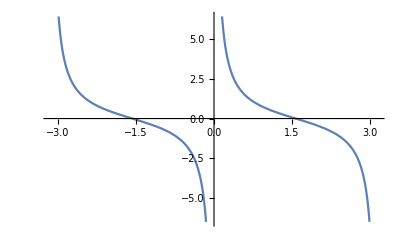

```mathematica
Plot[Cot[x],{x,-Pi,Pi}]
```